```mathematica
Smac=((ρon-ρoff)σon σoff)/((σon+σoff)(e+σon+σoff))Log[ρon/ρoff];
```

```mathematica
Smac2=Smac/.{ρon->B σoff}//FullSimplify
```

(σoff (-ρoff+B σoff) σon Log[(B σoff)/ρoff])/((σoff+σon) (e+σoff+σon))

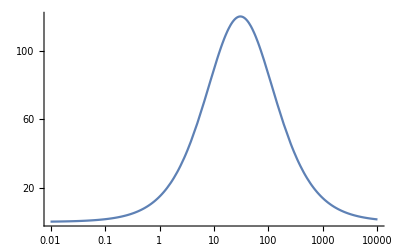

```mathematica
Plot[Smac2/.{B->74/30,σoff->30,e->1,ρoff->0.1},{σon,10^-2,10^4},ScalingFunctions->{"Log","Linear"}]
```

```mathematica
σontab=Table[{σon,Smac2}/.{B->74/30,σoff->30,e->1,ρoff->0.1,σon->10^x},{x,-2,4,0.1}]
```

{{0.01,0.157391},{0.0125893,0.19811},{0.0158489,0.249352},{0.0199526,0.313831},{0.0251189,0.394956},{0.0316228,0.497008},{0.0398107,0.625361},{0.0501187,0.786751},{0.0630957,0.98962},{0.0794328,1.24453},{0.1,1.56466},{0.125893,1.96646},{0.158489,2.47036},{0.199526,3.10169},{0.251189,3.89169},{0.316228,4.87868},{0.398107,6.10938},{0.501187,7.64018},{0.630957,9.53837},{0.794328,11.883},{1.,14.7651},{1.25893,18.2862},{1.58489,22.5554},{1.99526,27.6828},{2.51189,33.768},{3.16228,40.8842},{3.98107,49.0543},{5.01187,58.2218},{6.30957,68.219},{7.94328,78.7371},{10.,89.3106},{12.5893,99.327},{15.8489,108.073},{19.9526,114.821},{25.1189,118.943},{31.6228,120.025},{39.8107,117.958},{50.1187,112.951},{63.0957,105.499},{79.4328,96.2723},{100.,86.0067},{125.893,75.391},{158.489,64.9943},{199.526,55.2325},{251.189,46.3671},{316.228,38.5275},{398.107,31.7416},{501.187,25.9678},{630.957,21.1224},{794.328,17.1009},{1000.,13.7928},{1258.93,11.0906},{1584.89,8.89591},{1995.26,7.12148},{2511.89,5.69199},{3162.28,4.5437},{3981.07,3.62341},{5011.87,2.8872},{6309.57,2.2991},{7943.28,1.82986},{10000.,1.4558}}

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\sigma-on-tab-2.csv",σontab,"CSV"]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\sigma-on-tab-2.csv

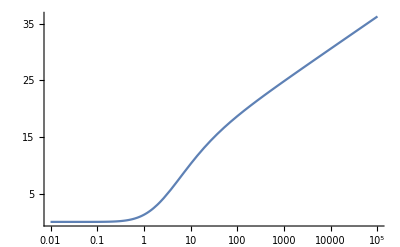

```mathematica
Plot[Smac2/.{B->74/30,σon->1,e->1,ρoff->0.1},{σoff,10^-2,10^5},ScalingFunctions->{"Log","Linear"},PlotRange->All]
```

```mathematica
σofftab=Table[{σoff,Smac2}/.{B->74/30,σon->1,e->1,ρoff->0.1,σoff->10^x},{x,-2,5,0.1}]
```

{{0.01,0.00051941},{0.0125893,0.000498091},{0.0158489,0.000442722},{0.0199526,0.000348668},{0.0251189,0.000220326},{0.0316228,0.0000824513},{0.0398107,6.13834×10^-7},{0.0501187,0.000116654},{0.0630957,0.000707998},{0.0794328,0.00228347},{0.1,0.00573249},{0.125893,0.0125477},{0.158489,0.0251409},{0.199526,0.0472629},{0.251189,0.0845152},{0.316228,0.144894},{0.398107,0.23924},{0.501187,0.381399},{0.630957,0.587821},{0.794328,0.876386},{1.,1.26437},{1.25893,1.76577},{1.58489,2.38851},{1.99526,3.13227},{2.51189,3.98773},{3.16228,4.93738},{3.98107,5.95789},{5.01187,7.02328},{6.30957,8.10809},{7.94328,9.18994},{10.,10.2511},{12.5893,11.2788},{15.8489,12.2654},{19.9526,13.2072},{25.1189,14.1036},{31.6228,14.9565},{39.8107,15.7688},{50.1187,16.5446},{63.0957,17.2879},{79.4328,18.003},{100.,18.6938},{125.893,19.3639},{158.489,20.0164},{199.526,20.6543},{251.189,21.2798},{316.228,21.8951},{398.107,22.5019},{501.187,23.1017},{630.957,23.6957},{794.328,24.2849},{1000.,24.8702},{1258.93,25.4524},{1584.89,26.0319},{1995.26,26.6093},{2511.89,27.1849},{3162.28,27.7591},{3981.07,28.3321},{5011.87,28.9042},{6309.57,29.4755},{7943.28,30.0462},{10000.,30.6163},{12589.3,31.1861},{15848.9,31.7555},{19952.6,32.3246},{25118.9,32.8935},{31622.8,33.4623},{39810.7,34.0308},{50118.7,34.5993},{63095.7,35.1677},{79432.8,35.736},{100000.,36.3042}}

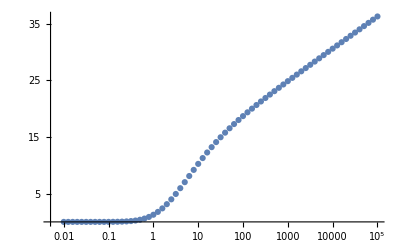

```mathematica
ListPlot[σofftab,ScalingFunctions->{"Log","Linear"}]
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\sigma-off-tab-2.csv",σofftab,"CSV"]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\sigma-off-tab-2.csv

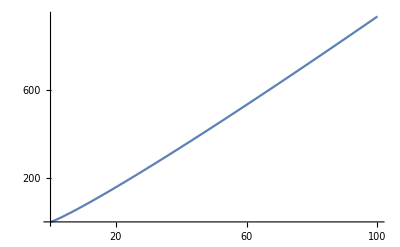

```mathematica
Plot[Smac2/.{σoff->30,σon->1,e->1,ρoff->0.1},{B,10^-2,10^2},ScalingFunctions->{"Linear","Linear"}]
```

```mathematica
Btab=Table[{B,Smac2}/.{σoff->30,σon->1,e->1,ρoff->0.1},{B,1,100,1}];
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\B-tab-2.csv",Btab,"CSV"]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\B-tab-2.csv

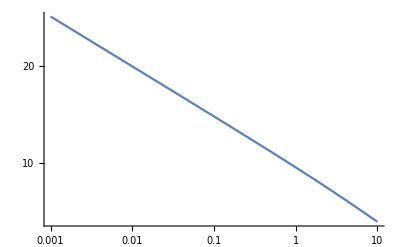

```mathematica
Plot[Smac2/.{σoff->30,σon->1,e->1,B->74/30},{ρoff,10^-3,10^1},ScalingFunctions->{"Log","Linear"}]
```

```mathematica
ρofftab=Table[{ρoff,Smac2}/.{σoff->30,σon->1,e->1,B->74/30,ρoff->10^x},{x,-3,1,0.1}]
```

{{0.001,25.0906},{0.00125893,24.5753},{0.00158489,24.0599},{0.00199526,23.5444},{0.00251189,23.029},{0.00316228,22.5135},{0.00398107,21.998},{0.00501187,21.4824},{0.00630957,20.9668},{0.00794328,20.4511},{0.01,19.9353},{0.0125893,19.4194},{0.0158489,18.9034},{0.0199526,18.3872},{0.0251189,17.8708},{0.0316228,17.3541},{0.0398107,16.8372},{0.0501187,16.3199},{0.0630957,15.8022},{0.0794328,15.2839},{0.1,14.7651},{0.125893,14.2455},{0.158489,13.725},{0.199526,13.2035},{0.251189,12.6807},{0.316228,12.1564},{0.398107,11.6304},{0.501187,11.1023},{0.630957,10.5718},{0.794328,10.0385},{1.,9.50192},{1.25893,8.96169},{1.58489,8.41727},{1.99526,7.86816},{2.51189,7.31391},{3.16228,6.75409},{3.98107,6.18845},{5.01187,5.61695},{6.30957,5.03993},{7.94328,4.45831},{10.,3.87383}}

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\rho-off-tab-2.csv",ρofftab,"CSV"]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\rho-off-tab-2.csv

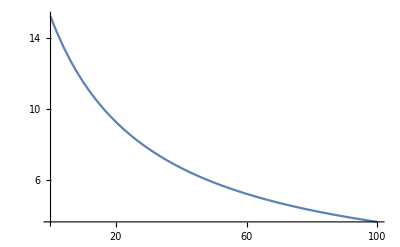

```mathematica
Plot[Smac2/.{σoff->30,σon->1,ρoff->1/10,B->74/30},{e,10^-2,10^2},ScalingFunctions->{"Linear","Linear"},PlotRange->All]
```

```mathematica
etab=Table[{e,Smac2}/.{σoff->30,σon->1,ρoff->1/10,B->74/30,e->10^x},{x,-2,2,0.1}]
```

{{0.01,15.2364},{0.0125893,15.2352},{0.0158489,15.2336},{0.0199526,15.2316},{0.0251189,15.229},{0.0316228,15.2258},{0.0398107,15.2218},{0.0501187,15.2168},{0.0630957,15.2104},{0.0794328,15.2024},{0.1,15.1923},{0.125893,15.1797},{0.158489,15.1638},{0.199526,15.1439},{0.251189,15.1189},{0.316228,15.0875},{0.398107,15.0481},{0.501187,14.9989},{0.630957,14.9373},{0.794328,14.8606},{1.,14.7651},{1.25893,14.6466},{1.58489,14.5},{1.99526,14.3197},{2.51189,14.0989},{3.16228,13.8305},{3.98107,13.5068},{5.01187,13.1202},{6.30957,12.6638},{7.94328,12.1326},{10.,11.524},{12.5893,10.8394},{15.8489,10.0852},{19.9526,9.27297},{25.1189,8.41931},{31.6228,7.54489},{39.8107,6.67247},{50.1187,5.82457},{63.0957,5.02129},{79.4328,4.27846},{100.,3.60673}}

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\e-tab-2.csv",etab,"CSV"]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\e-tab-2.csv